```mathematica
f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,2}])
```

-0.755297 ⅇ^((0.-0.515525 ⅈ) t)-1.52015 ⅇ^((0.+1.29156 ⅈ) t)

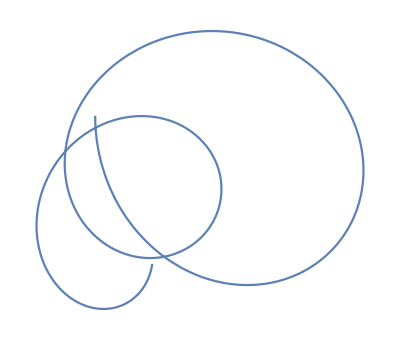

```mathematica
Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}]);
ParametricPlot[ReIm[%],{t,0,10},Axes->False]
```

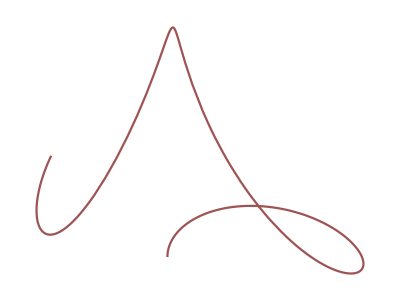
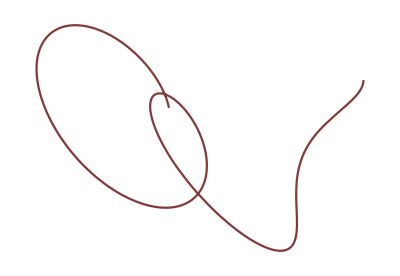
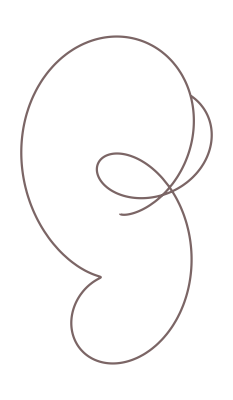
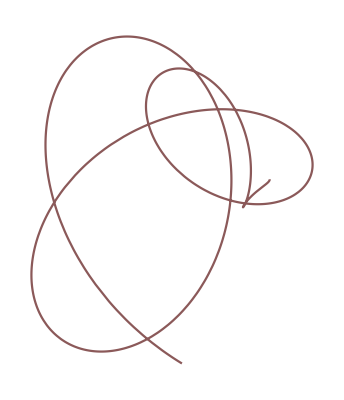
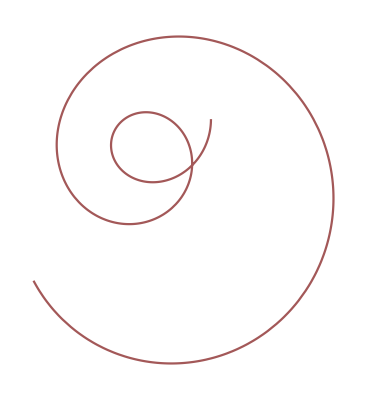
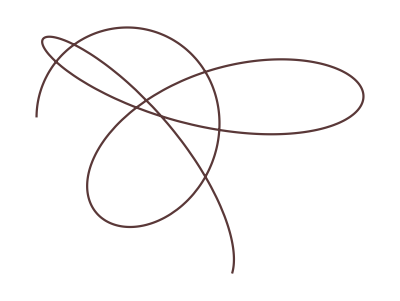
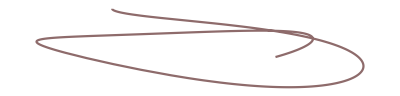
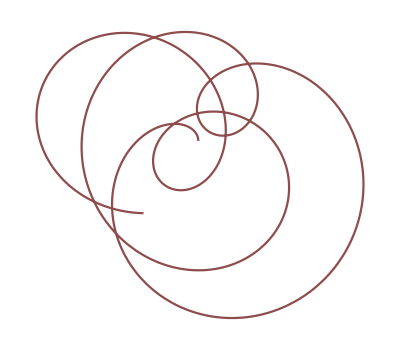

```mathematica
Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
max=First@Quiet@FindMaximum[{curv,0≤t≤10},{t,5}];
min=First@Quiet@FindMinimum[{curv,0≤t≤10},{t,5}];
ParametricPlot[ReIm[f],{t,0,10},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["CherryTones"][Rescale[curv,{min,max}]]],ColorFunctionScaling->False]],10]
```

```mathematica
curv/.t->3
```

0.0998075

```mathematica
Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}]);
curv=ArcCurvature[ReIm[%],t]
```

$Aborted

```mathematica
ComplexExpand[ReIm[a Exp[b I t]+c Exp[d I t]]]
```

{a Cos[b t]+c Cos[d t],a Sin[b t]+c Sin[d t]}

```mathematica
ArcCurvature[{Sum[Subscript[a, i] Cos[Subscript[b, i] t],{i,1,10}],Sum[Subscript[a, i] Sin[Subscript[b, i] t],{i,1,10}]},t]
```

$Aborted

```mathematica
[
```

```mathematica
ArcCurvature[{a Cos[b t],a Sin[b t]},t]
```

√((a^2 b^3 Cos[b t]^2+a b^2 c d Cos[b t] Cos[d t]+a b c d^2 Cos[b t] Cos[d t]+c^2 d^3 Cos[d t]^2+a^2 b^3 Sin[b t]^2+a b^2 c d Sin[b t] Sin[d t]+a b c d^2 Sin[b t] Sin[d t]+c^2 d^3 Sin[d t]^2)^2/(a^2 b^2 Cos[b t]^2+2 a b c d Cos[b t] Cos[d t]+c^2 d^2 Cos[d t]^2+a^2 b^2 Sin[b t]^2+2 a b c d Sin[b t] Sin[d t]+c^2 d^2 Sin[d t]^2)^3)